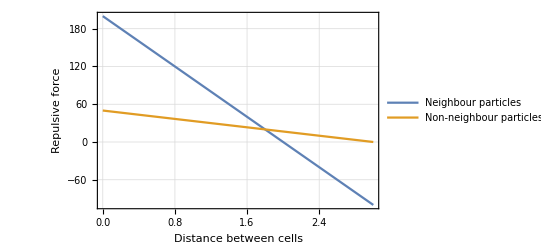

```mathematica
p1radius=p2radius=1;
springK= 100;
fRepulsion = 50;
range = 3;
fNeighbours[dr_]:=-(dr-(p1radius+p2radius))*springK;
fElse[dr_]:=
(*With[{ratio=(dr-p1radius-p2radius)/(range-p1radius-p2radius)},
-(fRepulsion*(1-ratio))
]*)
fRepulsion*(1-dr/range);
Plot[{fNeighbours[d],fElse[d]},{d,0,range},
PlotLegends->{"Neighbour particles","Non-neighbour particles"},
Frame->{{True,False},{True,False}},
GridLines->Automatic,
FrameLabel->{"Distance between cells","Repulsive force"}]
```

```mathematica
fElse[0]
```

150 (1-(-p1.radius-p2.radius)/(range-p1.radius-p2.radius))